```mathematica
Needs["MaTeX`"];
SetDirectory[NotebookDirectory[]];
```

```mathematica
Quit[]
```

## Free droplet

```mathematica
ClearAll[x]
```

```mathematica
Joutleft:=(Diff ⅇ^(R/lmin+x0/lplus) Jin (lmin+lplus)+c0out (ⅇ^(R/l)-ⅇ^(x0/l)) (Diff+lmin v) (Diff-lplus v))/(ⅇ^(x0/l) lplus (Diff+lmin v)+ⅇ^(R/l) lmin (Diff-lplus v))/.{lin->(linplus*linmin)/(linplus+linmin),l->(lplus*lmin)/(lplus+lmin)}/.{Diff->d}/.{linplus->2*d/(Sqrt[4*d*k+v^2]+v),linmin->2*d/(Sqrt[4*d*k+v^2]-v),lplus->2*d/(Sqrt[4*d*a+v^2]+v),lmin->2*d/(Sqrt[4*d*a+v^2]-v)};
Joutright:=(c0out (ⅇ^(L/l)-ⅇ^((R+x0)/l)) (Diff+lmin v) (Diff-lplus v))/(ⅇ^((R+x0)/l) lplus (Diff+lmin v)+ⅇ^(L/l) lmin (Diff-lplus v))/.{lin->(linplus*linmin)/(linplus+linmin),l->(lplus*lmin)/(lplus+lmin)}/.{Diff->d}/.{linplus->2*d/(Sqrt[4*d*k+v^2]+v),linmin->2*d/(Sqrt[4*d*k+v^2]-v),lplus->2*d/(Sqrt[4*d*a+v^2]+v),lmin->2*d/(Sqrt[4*d*a+v^2]-v)};
Jrad := -2 c0in Diff/lin Csch[ R/lin] Sinh[R/linmin] Sinh[R/linplus]/.{lin->(linplus*linmin)/(linplus+linmin),l->(lplus*lmin)/(lplus+lmin)}/.{Diff->d}/.{linplus->2*d/(Sqrt[4*d*k+v^2]+v),linmin->2*d/(Sqrt[4*d*k+v^2]-v),lplus->2*d/(Sqrt[4*d*a+v^2]+v),lmin->2*d/(Sqrt[4*d*a+v^2]-v)};
Jpos:=1/(linmin linplus)2 c0in Csch[ R/lin] (linmin (-Diff+linplus v) Cosh[R/linplus] Sinh[R/linmin]+linplus (Diff+linmin v) Cosh[R/linmin] Sinh[R/linplus])/.{Diff->d}/.{lin->(linplus*linmin)/(linplus+linmin),l->(lplus*lmin)/(lplus+lmin)}/.{linplus->2*d/(Sqrt[4*d*k+v^2]+v),linmin->2*d/(Sqrt[4*d*k+v^2]-v),lplus->2*d/(Sqrt[4*d*a+v^2]+v),lmin->2*d/(Sqrt[4*d*a+v^2]-v)};
cin=c0in ⅇ^(-x/linmin-x0/linplus) Csch[(1/linmin+1/linplus) R] (ⅇ^((1/linmin+1/linplus) x) Sinh[R/linmin]+ⅇ^((1/linmin+1/linplus) x0) Sinh[R/linplus])/.{Diff->d}/.{lin->(linplus*linmin)/(linplus+linmin),l->(lplus*lmin)/(lplus+lmin)}/.{linplus->2*d/(Sqrt[4*d*k+v^2]+v),linmin->2*d/(Sqrt[4*d*k+v^2]-v),lplus->2*d/(Sqrt[4*d*a+v^2]+v),lmin->2*d/(Sqrt[4*d*a+v^2]-v)};
coutleft:=(ⅇ^(-x/lmin) (-(ⅇ^(((lmin+lplus) (R+x))/(lmin lplus))-ⅇ^((1/lmin+1/lplus) x0)) Jin lmin lplus+c0out ⅇ^(R/lplus+x0/lmin) (ⅇ^((1/lmin+1/lplus) x) lplus (Diff+lmin v)+lmin (Diff-lplus v))))/(ⅇ^((1/lmin+1/lplus) x0) lplus (Diff+lmin v)+ⅇ^((1/lmin+1/lplus) R) lmin (Diff-lplus v))/.{lin->(linplus*linmin)/(linplus+linmin),l->(lplus*lmin)/(lplus+lmin)}/.{Diff->d}/.{linplus->2*d/(Sqrt[4*d*k+v^2]+v),linmin->2*d/(Sqrt[4*d*k+v^2]-v),lplus->2*d/(Sqrt[4*d*a+v^2]+v),lmin->2*d/(Sqrt[4*d*a+v^2]-v)};
coutright:=(c0out ⅇ^((R-x+x0)/lmin) (ⅇ^((1/lmin+1/lplus) x) lplus (Diff+lmin v)+ⅇ^(L (1/lmin+1/lplus)) lmin (Diff-lplus v)))/(ⅇ^(((lmin+lplus) (R+x0))/(lmin lplus)) lplus (Diff+lmin v)+ⅇ^(L (1/lmin+1/lplus)) lmin (Diff-lplus v))/.{lin->(linplus*linmin)/(linplus+linmin),l->(lplus*lmin)/(lplus+lmin)}/.{Diff->d}/.{linplus->2*d/(Sqrt[4*d*k+v^2]+v),linmin->2*d/(Sqrt[4*d*k+v^2]-v),lplus->2*d/(Sqrt[4*d*a+v^2]+v),lmin->2*d/(Sqrt[4*d*a+v^2]-v)};
cmin:=1/linmin c0in ⅇ^((linplus (Log[linmin]-Log[linplus]+Log[Sinh[R/linmin]]-Log[Sinh[R/linplus]]))/(linmin+linplus)) (linmin+linplus) Csch[(1/linmin+1/linplus) R] Sinh[R/linplus]/.{Diff->d}/.{linplus->2*d/(Sqrt[4*d*k+v^2]+v),linmin->2*d/(Sqrt[4*d*k+v^2]-v),lplus->2*d/(Sqrt[4*d*a+v^2]+v),lmin->2*d/(Sqrt[4*d*a+v^2]-v)};
```

```mathematica
dRdt[R_,x0_]:=Jrad+(Joutleft-Joutright);
dxdt[R_,x0_]:=Jpos-(Joutleft+Joutright);
```

### No decay

```mathematica
params={d->1.0,k->0.1,a->0.0,c0out->0.1,c0in->0.9}
```

{d→1.,k→0.1,a→0.,c0out→0.1,c0in→0.9}

```mathematica
FullSimplify[dRdt[R,x]/.a->0,v>0]
```

Jin+c0in √(4 d k+v^2) (Cosh[(R v)/d]-Cosh[(R √(4 d k+v^2))/d]) Csch[(R √(4 d k+v^2))/d]

```mathematica
Rstable[J_,vin_,paramsin_]:=FindRoot[Jin+c0in √(4 d k+v^2) (Cosh[(R v)/d]-Cosh[(R √(4 d k+v^2))/d]) Csch[(R √(4 d k+v^2))/d]/.paramsin/.{Jin->J,v->vin},{R,10^-5}]
```

```mathematica
FullSimplify[dxdt[R,x]/.a->0,v>0]
```

-Jin+c0in v+c0in √(4 d k+v^2) Csch[(R √(4 d k+v^2))/d] Sinh[(R v)/d]

```mathematica
Xstable[J_,vin_,paramsin_]:=-Jin+c0in v+c0in √(4 d k+v^2) Csch[(R √(4 d k+v^2))/d] Sinh[(R v)/d]/.Rstable[J,vin,paramsin]/.paramsin/.{Jin->J,v->vin}
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

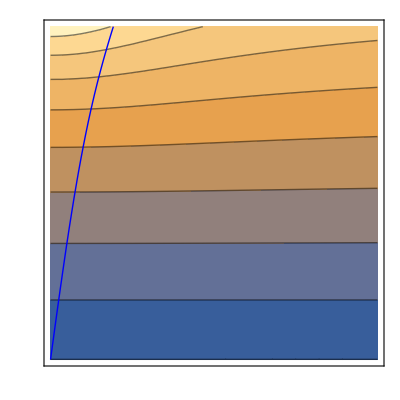

```mathematica
p1=ContourPlot[(R/.Rstable[J,v,params]),{v,0,2},{J,0,0.5},Mesh->{{0}},MeshFunctions->{Xstable[#2,#1,params]&},MeshStyle->{Blue,Thick},
PlotLabel->MaTeX["\\text{Stable droplet radius}",Magnification->2],
PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendMarkerSize->250,LegendLabel->MaTeX["R",Magnification->2]],Right]}, 
Frame->True,
PlotRangePadding->0,
FrameStyle->BlackFrame,
FrameLabel->{MaTeX["v",Magnification->2],MaTeX["J_{in}",Magnification->2]},
FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,0.5,0.1]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,2.0,0.5]}],None}},
RotateLabel->False,
Axes->True]
```

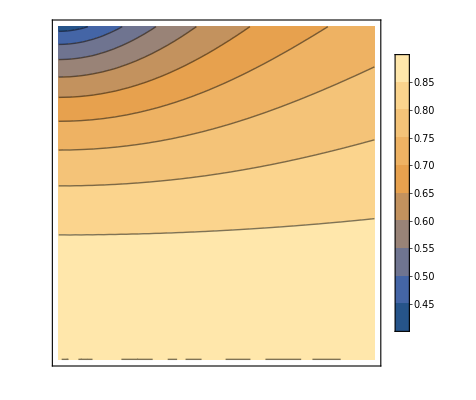

```mathematica
p1=ContourPlot[cmin/.params/.Rstable[J,v,params],{v,0,2},{J,0,0.5},
PlotLabel->MaTeX["\\text{Minimum concentration}",Magnification->2],
PlotLegends->{Placed[BarLegend[Automatic,Automatic],Right]}, 
Frame->True,
PlotRangePadding->0,
FrameStyle->BlackFrame,
FrameLabel->{MaTeX["v",Magnification->2],MaTeX["J_{in}",Magnification->2]},
FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,0.5,0.1]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,2.0,0.5]}],None}},
RotateLabel->False,
Axes->True]
```

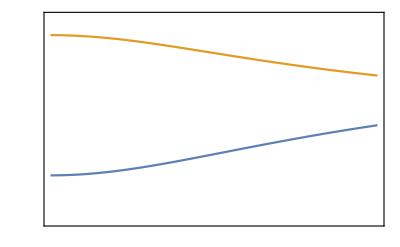

```mathematica
Jplot=0.3;
normR=R/.Rstable[Jplot,0,params]/.J->Jplot;
p=Plot[{(cmin/c0in/.params/.Rstable[Jplot,v,params]/.J->Jplot),(R/.Rstable[Jplot,v,params]/.J->Jplot)/normR},{v,0,2} ,
PlotLegends->{MaTeX["c_{\\text{min}}/c_0^+",Magnification->2],MaTeX["R_{\\text{stable}}/R_{\\text{stable}}(v=0)",Magnification->2]},
PlotLabel->MaTeX["\\text{Stable droplet radius}",Magnification->2],
Frame->True,
PlotRangePadding->0,
FrameStyle->BlackFrame,
FrameLabel->{MaTeX["v",Magnification->2]},
FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0.8,1.0,0.1]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,2.0,0.5]}],None}},
RotateLabel->False,
Axes->True,
PlotRange->{{0,2},{0.8,1.02}}]
```

```mathematica
Export["advectioneffect.pdf",p]
```

advectioneffect.pdf

### Free droplet - with decay

```mathematica
ClearAll[Stable,dxdtplot, dRdtplot]
```

```mathematica
params={d->1.,k->0.3,a->0.1,c0out->0.1,c0in->0.9,L->5}
```

{d→1.,k→0.3,a→0.1,c0out→0.1,c0in→0.9,L→5}

```mathematica
Stable[J_,vin_,paramsin_]:=FindRoot[{dRdt[R,x0]/.paramsin/.{Jin->J,v->vin},dxdt[R,x0]/.paramsin/.{Jin->J,v->vin}},{R,10^-2,10^-2,2.5},{x0,10^-2,10^-2,5}]
```

FindRoot::reged: The point {0.01,0.01} is at the edge of the search region {0.01,2.5} in coordinate 1 and the computed search direction points outside the region.

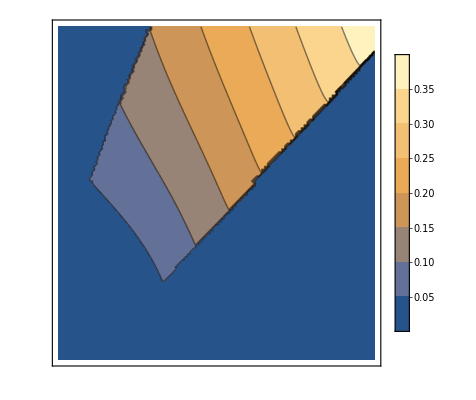

```mathematica
p=ContourPlot[R/.Stable[J,v,params],{v,0,0.15},{J,0,0.25},
PlotLabel->MaTeX["\\text{Stable radius}",Magnification->2],
PlotLegends->{Placed[BarLegend[Automatic,Automatic, LegendMarkerSize->250],Right]}, 
Frame->True,
PlotRangePadding->0,
FrameStyle->BlackFrame,
FrameLabel->{MaTeX["v",Magnification->2],MaTeX["J_{in}",Magnification->2]},
FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,0.3,0.05]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,0.15,0.05]}],None}},
RotateLabel->False,
Axes->True]
```

```mathematica
Export["Rstable.pdf",p]
```

Rstable.pdf

FindRoot::reged: The point {0.01,0.01} is at the edge of the search region {0.01,2.5} in coordinate 1 and the computed search direction points outside the region.

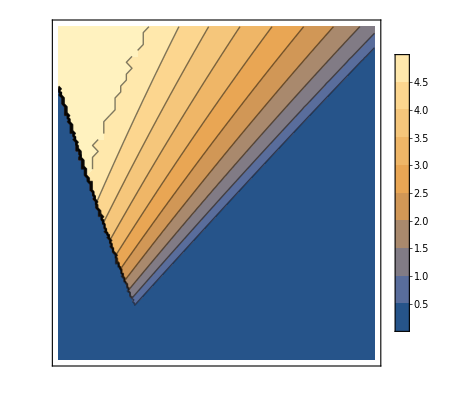

```mathematica
p2=ContourPlot[x0/.Stable[J,v,params],{v,0,0.15},{J,0,0.25},
PlotLabel->MaTeX["\\text{Stable position}",Magnification->2],
PlotLegends->{Placed[BarLegend[Automatic,Automatic, LegendMarkerSize->250],Right]}, 
Frame->True,
PlotRangePadding->0,
FrameStyle->BlackFrame,
FrameLabel->{MaTeX["v",Magnification->2],MaTeX["J_{in}",Magnification->2]},
FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,0.3,0.05]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,0.15,0.05]}],None}},
RotateLabel->False,
Axes->True]
```

```mathematica
Export["Xstable.pdf",p2]
```

Xstable.pdf

```mathematica
vplot=0.10;
Jplot=0.18;
```

```mathematica
dxdtplot[R_,x0_,vin_,J_]=dxdt[R,x0]/.params/.{v->vin,Jin->J};
dRdtplot[R_,x0_,vin_,J_]=dRdt[R,x0]/.params/.{v->vin,Jin->J};
```

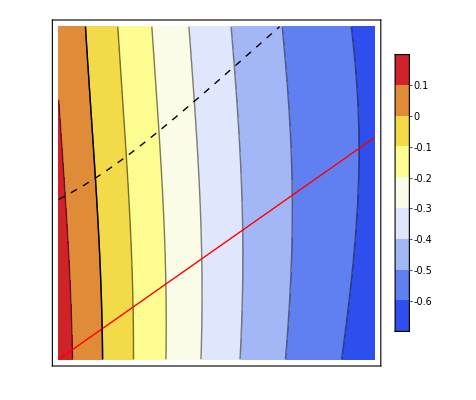

```mathematica
p3=ContourPlot[dRdt[R,x0]/.params/.{v->vplot,Jin->Jplot},{R,0,2},{x0,0,3},PlotLegends->Automatic,Mesh->{{0},{0}},MeshFunctions->{dxdtplot[#1,#2,vplot,Jplot]&,dRdtplot[#1,#2,vplot,Jplot]&,#2-#1&},MeshStyle->{{Black, Thick, Dashed},{Black, Thick},{Red}},ColorFunction->"TemperatureMap",PlotLabel->MaTeX["dR/dt",Magnification->2],
PlotLegends->{Placed[BarLegend[Automatic,Automatic, LegendMarkerSize->250],Right]}, 
Frame->True,
PlotRangePadding->0,
FrameStyle->BlackFrame,
FrameLabel->{MaTeX["R",Magnification->2],MaTeX["x_0",Magnification->2]},
FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,3,0.5]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,2,0.5]}],None}},
RotateLabel->False,
Axes->True]
```

```mathematica
Export["dRdt.pdf",p3]
```

dRdt.pdf

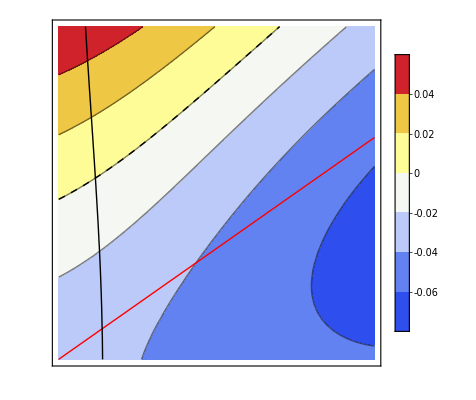

```mathematica
p4=ContourPlot[dxdt[R,x0]/.params/.{v->vplot,Jin->Jplot},{R,0,2},{x0,0,3},PlotLegends->Automatic,Mesh->{{0},{0},{0}},MeshFunctions->{dxdtplot[#1,#2,vplot,Jplot]&,dRdtplot[#1,#2,vplot,Jplot]&,#2-#1&},MeshStyle->{{Black, Thick, Dashed},{Black, Thick},{Red}},ColorFunction->"TemperatureMap",PlotLabel->MaTeX["dx_{0}/dt",Magnification->2],
PlotLegends->{Placed[BarLegend[Automatic,Automatic, LegendMarkerSize->250],Right]}, 
Frame->True,
PlotRangePadding->0,
FrameStyle->BlackFrame,
FrameLabel->{MaTeX["R",Magnification->2],MaTeX["x_{0}",Magnification->2]},
FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,3,0.5]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,2,0.5]}],None}},
RotateLabel->False,
Axes->True]
```

```mathematica
Export["dXdt.pdf",p4]
```

dXdt.pdf

```mathematica
vplot2=0.08
```

0.08

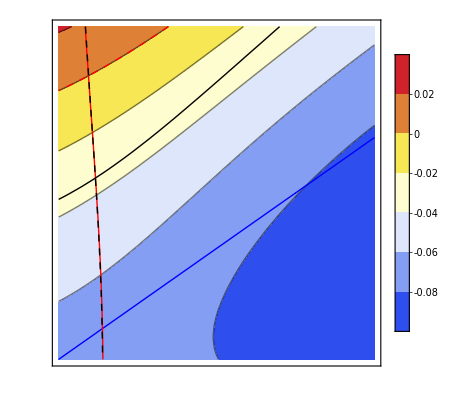

0

0

```mathematica
ContourPlot[dxdt[R,x0]/.params/.{v->vplot2,Jin->Jplot},{R,0,2},{x0,0,3},PlotLegends->Automatic,Mesh->{{0},{0},{0}},MeshFunctions->{dxdtplot[#1,#2,vplot,Jplot]&,dRdtplot[#1,#2,vplot,Jplot]&,dxdtplot[#1,#2,vplot2,Jplot]&,dRdtplot[#1,#2,vplot2,Jplot]&,#2-#1&},MeshStyle->{{Black, Thick},{Black, Thick, Dashed},{Red, Thick, Dashed}, {Red, Thick},{Blue}},ColorFunction->"TemperatureMap",PlotLabel->MaTeX["dx_{0}/dt",Magnification->2],
PlotLegends->{Placed[BarLegend[Automatic,Automatic, LegendMarkerSize->250],Right]}, 
Frame->True,
PlotRangePadding->0,
FrameStyle->BlackFrame,
FrameLabel->{MaTeX["R",Magnification->2],MaTeX["x_{0}",Magnification->2]},
FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,3,0.5]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,2,0.5]}],None}},
RotateLabel->False,
Axes->True]
```

```mathematica
vplot=0.1;
vplot2=0.08;
Jplot=0.18;
```

{d→1.,k→0.3,a→0.1,c0out→0.1,c0in→0.9,L→5}

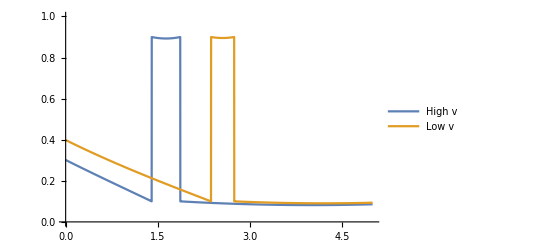

```mathematica
params={d->1.,k->0.3,a->0.1,c0out->0.1,c0in->0.9,L->5}
x0stable=x0/.Stable[Jplot,vplot,params];
radstable=R/.Stable[Jplot,vplot,params];
functionList={coutleft/.params/.{x0->x0stable,R->radstable}/.{v->vplot,Jin->Jplot},cin/.params/.{x0->x0stable,R->radstable}/.{v->vplot,Jin->Jplot},coutright/.params/.{x0->x0stable,R->radstable}/.{v->vplot,Jin->Jplot}};
nodes={0,x0stable-radstable,x0stable+radstable,L/.params};
f[x_]=Piecewise[Transpose[{functionList,#1≤x≤#2&@@@Partition[nodes,2,1]}]];

x0stable2=x0/.Stable[Jplot,vplot2,params];
radstable2=R/.Stable[Jplot,vplot2,params];
functionList2={coutleft/.params/.{x0->x0stable2,R->radstable2}/.{v->vplot2,Jin->Jplot},cin/.params/.{x0->x0stable2,R->radstable2}/.{v->vplot2,Jin->Jplot},coutright/.params/.{x0->x0stable2,R->radstable2}/.{v->vplot2,Jin->Jplot}};
nodes2={0,x0stable2-radstable2,x0stable2+radstable2,L/.params};
g[x_]=Piecewise[Transpose[{functionList2,#1≤x≤#2&@@@Partition[nodes2,2,1]}]];

Plot[{f[x],g[x]},{x,0,5},Exclusions->None,PlotRange->{0,1},PlotLegends->{"High v","Low v"}]
```

## Droplet stuck to sides

```mathematica
dRdtleft=(Diff ⅇ^(R/linplus) Jin (linmin+linplus)-c0in (-1+ⅇ^((1/linmin+1/linplus) R)) (Diff+linmin v) (Diff-linplus v))/(ⅇ^((1/linmin+1/linplus) R) linplus (Diff+linmin v)+linmin (Diff-linplus v))-(c0out (ⅇ^(L (1/lmin+1/lplus))-ⅇ^((1/lmin+1/lplus) R)) (Diff+lmin v) (Diff-lplus v))/(ⅇ^((1/lmin+1/lplus) R) lplus (Diff+lmin v)+ⅇ^(L (1/lmin+1/lplus)) lmin (Diff-lplus v))/.{Diff->d};
dRdtright=-(c0in (-1+ⅇ^((1/linmin+1/linplus) R)) (Diff+linmin v) (Diff-linplus v))/(linplus (Diff+linmin v)+ⅇ^((1/linmin+1/linplus) R) linmin (Diff-linplus v))+(Diff ⅇ^(L/lplus+R/lmin) Jin (lmin+lplus)-c0out (ⅇ^(L (1/lmin+1/lplus))-ⅇ^((1/lmin+1/lplus) R)) (Diff+lmin v) (Diff-lplus v))/(ⅇ^(L (1/lmin+1/lplus)) lplus (Diff+lmin v)+ⅇ^((1/lmin+1/lplus) R) lmin (Diff-lplus v))/.{Diff->d};
```

```mathematica
dR1dt:=-c0out v-1/2 c0out (v+√(4 a Diff+v^2)) (-1+(ⅇ^((L (-v+√(4 a Diff+v^2)))/(2 Diff)) (ⅇ^((L (v+√(4 a Diff+v^2)))/(2 Diff))-ⅇ^(((R1+R2) (v+√(4 a Diff+v^2)))/(2 Diff))) (-v+√(4 a Diff+v^2)) ((2 Diff)/(-v+√(4 a Diff+v^2))+(2 Diff)/(v+√(4 a Diff+v^2))))/(2 Diff (-ⅇ^(((R1+R2) (-v+√(4 a Diff+v^2)) (v+√(4 a Diff+v^2)) ((2 Diff)/(-v+√(4 a Diff+v^2))+(2 Diff)/(v+√(4 a Diff+v^2))))/(4 Diff^2))+ⅇ^(L ((-v+√(4 a Diff+v^2))/(2 Diff)+(v+√(4 a Diff+v^2))/(2 Diff))))))+(Diff ⅇ^((R1 (v+√(4 Diff k+v^2)))/(2 Diff)) Jin ((2 Diff)/(-v+√(4 Diff k+v^2))+(2 Diff)/(v+√(4 Diff k+v^2)))-c0in (-1+ⅇ^(R1 ((-v+√(4 Diff k+v^2))/(2 Diff)+(v+√(4 Diff k+v^2))/(2 Diff)))) (Diff+(2 Diff v)/(-v+√(4 Diff k+v^2))) (Diff-(2 Diff v)/(v+√(4 Diff k+v^2))))/((2 Diff ⅇ^(R1 ((-v+√(4 Diff k+v^2))/(2 Diff)+(v+√(4 Diff k+v^2))/(2 Diff))) (Diff+(2 Diff v)/(-v+√(4 Diff k+v^2))))/(v+√(4 Diff k+v^2))+(2 Diff (Diff-(2 Diff v)/(v+√(4 Diff k+v^2))))/(-v+√(4 Diff k+v^2)))/.{Diff->d}
dR2dt:=(c0out (-v+√(4 a Diff+v^2)) (Diff+(2 Diff v)/(-v+√(4 a Diff+v^2))-(ⅇ^((L (v+√(4 a Diff+v^2)))/(2 Diff)) (ⅇ^((L (-v+√(4 a Diff+v^2)))/(2 Diff))-ⅇ^(((R1+R2) (-v+√(4 a Diff+v^2)))/(2 Diff))) (v+√(4 a Diff+v^2)) ((2 Diff)/(-v+√(4 a Diff+v^2))+(2 Diff)/(v+√(4 a Diff+v^2))))/(2 (-ⅇ^(((R1+R2) (-v+√(4 a Diff+v^2)) (v+√(4 a Diff+v^2)) ((2 Diff)/(-v+√(4 a Diff+v^2))+(2 Diff)/(v+√(4 a Diff+v^2))))/(4 Diff^2))+ⅇ^(L ((-v+√(4 a Diff+v^2))/(2 Diff)+(v+√(4 a Diff+v^2))/(2 Diff)))))))/(2 Diff)-(c0in (-1+ⅇ^(R2 ((-v+√(4 Diff k+v^2))/(2 Diff)+(v+√(4 Diff k+v^2))/(2 Diff)))) (Diff+(2 Diff v)/(-v+√(4 Diff k+v^2))) (Diff-(2 Diff v)/(v+√(4 Diff k+v^2))))/((2 Diff (Diff+(2 Diff v)/(-v+√(4 Diff k+v^2))))/(v+√(4 Diff k+v^2))+(2 Diff ⅇ^(R2 ((-v+√(4 Diff k+v^2))/(2 Diff)+(v+√(4 Diff k+v^2))/(2 Diff))) (Diff-(2 Diff v)/(v+√(4 Diff k+v^2))))/(-v+√(4 Diff k+v^2)))/.{Diff->d}
```

```mathematica
params={d->1.0,k->0.3,a->0.1,c0out->0.1,c0in->0.9,L->5}
```

{d→1.,k→0.3,a→0.1,c0out→0.1,c0in→0.9,L→5}

```mathematica
RleftStable[vin_,J_,paramsin_]:=FindRoot[dRdtleft/.{linplus->2*d/(Sqrt[4*d*k+v^2]+v),linmin->2*d/(Sqrt[4*d*k+v^2]-v),lplus->2*d/(Sqrt[4*d*a+v^2]+v),lmin->2*d/(Sqrt[4*d*a+v^2]-v)}/.paramsin/.{v->vin,Jin->J},{R,0}][[1,2]]
RrightStable[vin_,J_,paramsin_]:=FindRoot[dRdtright/.{linplus->2*d/(Sqrt[4*d*k+v^2]+v),linmin->2*d/(Sqrt[4*d*k+v^2]-v),lplus->2*d/(Sqrt[4*d*a+v^2]+v),lmin->2*d/(Sqrt[4*d*a+v^2]-v)}/.paramsin/.{v->vin,Jin->J},{R,0}][[1,2]]
R12Stable[vin_,J_,paramsin_]:=FindRoot[{dR1dt/.{linplus->2*d/(Sqrt[4*d*k+v^2]+v),linmin->2*d/(Sqrt[4*d*k+v^2]-v),lplus->2*d/(Sqrt[4*d*a+v^2]+v),lmin->2*d/(Sqrt[4*d*a+v^2]-v)}/.paramsin/.{v->vin,Jin->J},dR2dt/.{linplus->2*d/(Sqrt[4*d*k+v^2]+v),linmin->2*d/(Sqrt[4*d*k+v^2]-v),lplus->2*d/(Sqrt[4*d*a+v^2]+v),lmin->2*d/(Sqrt[4*d*a+v^2]-v)}/.paramsin/.{v->vin,Jin->J}},{R1,0},{R2,0}]
```

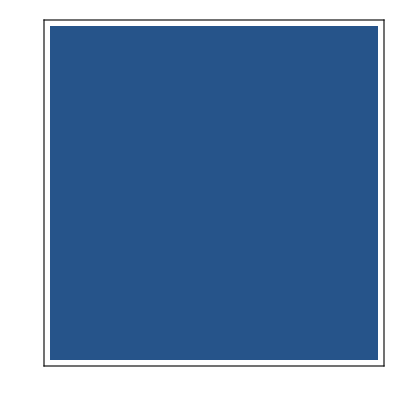

```mathematica
p5=DensityPlot[{0},{v,0,1},{J,0,0.25}, Mesh->{{0,0}},MeshFunctions->{R12Stable[#1,#2,params][[1,2]]&,R12Stable[#1,#2,params][[2,2]]&,RleftStable[#1,#2,params]&,RrightStable[#1,#2,params]&},MeshStyle->{{Black, Dashed, Thick},{Black,DotDashed, Thick},{Red, Thick},{Red, Thick, Dashed}},PlotLabel->MaTeX["\\text{Stable droplet radius}",Magnification->2],
Frame->True,
PlotRangePadding->0,
FrameStyle->BlackFrame,
FrameLabel->{MaTeX["v",Magnification->2],MaTeX["J_{in}",Magnification->2]},
FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,0.25,0.05]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,1.0,0.25]}],None}},
RotateLabel->False,
Axes->True]
```

```mathematica
Export["Numericalphase.pdf",p5]
```

Numericalphase.pdf

```mathematica
JminrightED=Flatten[Solve[(-2 a c0out d (-1+ⅇ^((L √(4 a d+v^2))/d))+2 ⅇ^((L (v+√(4 a d+v^2)))/(2 d)) Jin √(4 a d+v^2))/((-1+ⅇ^((L √(4 a d+v^2))/d)) v+(1+ⅇ^((L √(4 a d+v^2))/d)) √(4 a d+v^2))==0,Jin]//FullSimplify][[1,2]]
```

(a c0out d ⅇ^(-(L (v+√(4 a d+v^2)))/(2 d)) (-1+ⅇ^((L √(4 a d+v^2))/d)))/(√(4 a d+v^2))

```mathematica
JminleftED=Flatten[Solve[Jin+(2 a c0out d)/(v-√(4 a d+v^2) Coth[(L √(4 a d+v^2))/(2 d)])==0,Jin]//FullSimplify][[1,2]]
```

-(2 a c0out d)/(v-√(4 a d+v^2) Coth[(L √(4 a d+v^2))/(2 d)])

```mathematica
Jmin2Drop=1/2 c0out (v+((1+ⅇ^((L √(4 a d+v^2))/d)-2 ⅇ^((L (-v+√(4 a d+v^2)))/(2 d))) √(4 a d+v^2))/(-1+ⅇ^((L √(4 a d+v^2))/d)));
```

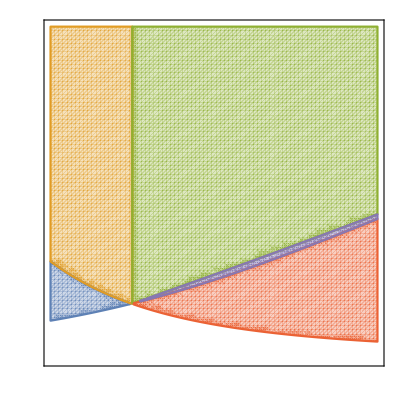

```mathematica
paramsphasediag={d->1.,k->0.3,a->0.1,L->5,c0out->0.1,c0in->0.9};
vcross=a*L/2;
p7=RegionPlot[{J>(JminleftED/.paramsphasediag)&&v<(vcross/.paramsphasediag) &&J<(JminrightED/.paramsphasediag),
J>(JminrightED/.paramsphasediag)&&v<(vcross/.paramsphasediag),
J>(Jmin2Drop/.paramsphasediag)&&v>(vcross/.paramsphasediag),
J>(JminrightED/.paramsphasediag)&&J<(JminleftED/.paramsphasediag),
J>(JminleftED/.paramsphasediag)&&J<(Jmin2Drop/.paramsphasediag)&&v>(vcross/.paramsphasediag)},
{v,0,1},{J,0,0.25},PlotPoints->80,
Epilog->{Text[MaTeX["\\text{Right}",Magnification->1.3],Scaled[{.85,.2}]],
Text[MaTeX["\\text{Left and right, Left, Right}",Magnification->1.3],Scaled[{.65,.6}]],
Text[MaTeX["\\text{Left}",Magnification->1.3],Scaled[{.08,.18}]],
Text[MaTeX["\\text{No droplets}",Magnification->1.3],Scaled[{.25,.08}]],
Text[MaTeX["\\text{Left or right}",Magnification->1.3],Scaled[{.2,.8}]],
Text[MaTeX["\\text{Left or right}",Magnification->1.3],Scaled[{.68,.3}]]},
Frame->True,
PlotRangePadding->0,
FrameStyle->BlackFrame,
FrameLabel->{MaTeX["v",Magnification->2],MaTeX["J_{in}",Magnification->2]},
FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,0.25,0.05]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,1.0,0.25]}],None}},
RotateLabel->False,
Axes->True]
```

```mathematica
Export["phaseapprox.pdf",p7]
```

phaseapprox.pdf

```mathematica
IPdilute=1/6 (3 c0in+3 c0out+√3 (-c0in+c0out));
IPdense=1/6 (3 c0in+√3 (c0in-c0out)+3 c0out);
```

```mathematica
Jminright=Flatten[Solve[(ⅇ^((L (v+√(4 a d+v^2)))/(2 d)) Jin √(4 a d+v^2))/(a d (-1+ⅇ^((L √(4 a d+v^2))/d)))==IPdilute,Jin]//FullSimplify][[1,2]]
```

-(a ((-3+√3) c0in-(3+√3) c0out) d ⅇ^(-(L (v+√(4 a d+v^2)))/(2 d)) (-1+ⅇ^((L √(4 a d+v^2))/d)))/(6 √(4 a d+v^2))

```mathematica
Jminleft=Flatten[Solve[-(Jin (v-√(4 a d+v^2) Coth[(L √(4 a d+v^2))/(2 d)]))/(2 a d)==IPdilute,Jin]//FullSimplify][[1,2]]
```

(a ((-3+√3) c0in-(3+√3) c0out) d)/(3 (v-√(4 a d+v^2) Coth[(L √(4 a d+v^2))/(2 d)]))

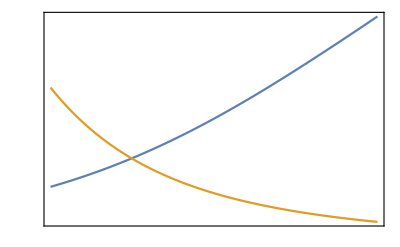

```mathematica
p8=Plot[{Jminleft/.params,Jminright/.params},{v,0,1},
Frame->True,
PlotRangePadding->0,
FrameStyle->BlackFrame,
FrameLabel->{MaTeX["v",Magnification->2],MaTeX["J_{in}",Magnification->2]},
FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,0.3,0.05]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,1.0,0.25]}],None}},
RotateLabel->False,
Axes->True]
```

```mathematica
Export["Jmin.pdf",p8]
```

Jmin.pdf

```mathematica
params={d->1.0,k->0.3,a->0.1,c0out->0.1,c0in->0.9,L->5}
```

{d→1.,k→0.3,a→0.1,c0out→0.1,c0in→0.9,L→5}

```mathematica
f[c_]=(c-c0out)^2*(c-c0in)^2
```

(c-c0in)^2 (c-c0out)^2

```mathematica
IPdilute=1/6 (3 c0in+3 c0out+√3 (-c0in+c0out));
IPdense=1/6 (3 c0in+√3 (c0in-c0out)+3 c0out);
```

```mathematica
functionList={f[c]/.params,f[c]/.params,f[c]/.params};
nodes={0,IPdilute/.params,IPdense/.params,1};

g[x_]=Piecewise[Transpose[{functionList,#1≤x≤#2&@@@Partition[nodes,2,1]}]]
```

Piecewise[{{(-0.9+c)^2 (-0.1+c)^2, 0≤x≤0.26906||0.26906≤x≤0.73094||0.73094≤x≤1}, {0, True}}]

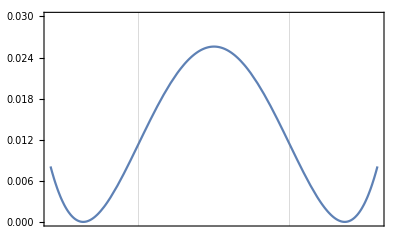

```mathematica
p8=Plot[f[c]/.params,{c,0,1},
Frame->True,
PlotRangePadding->0,
FrameStyle->BlackFrame,
FrameLabel->{MaTeX["c",Magnification->2],MaTeX["f",Magnification->2]},
FrameTicks->{{},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,1.0,0.2]}],None}},
RotateLabel->False,
Axes->True,
GridLines->{{{IPdense/.params,{Black,Thick,Dashed}},{IPdilute/.params,{Black,Thick,Dashed}}},{}},
PlotRange->{{0,1},{0,0.03}}]
```

```mathematica
Export["Freeenergydensity.pdf",p8]
```

Freeenergydensity.pdf